```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Inport data *)
NamData0=Import["RAW_data/MaxLik_OUTPUT_TNLCd_anal_test_BestPerm_wait_TT6.txt","Table"];
```

```mathematica
Rho[i_,NamData0_]:={{NamData0[[4+16i,1]],NamData0[[5+16i,1]]},{NamData0[[6+16i,1]],NamData0[[7+16i,1]]}}+{{NamData0[[9+16i,1]],NamData0[[10+16i,1]]},{NamData0[[11+16i,1]],NamData0[[12+16i,1]]}}*I
```

```mathematica
RhoListALL=ParallelTable[Rho[i,NamData0],{i,0,NamData0[[1,1]]-1}];
```

```mathematica
RhoListH=ParallelTable[Rho[i,NamData0],{i,0,NamData0[[1,1]]-1,6}];
RhoListV=ParallelTable[Rho[i,NamData0],{i,1,NamData0[[1,1]]-1,6}];
RhoListD=ParallelTable[Rho[i,NamData0],{i,2,NamData0[[1,1]]-1,6}];
RhoListA=ParallelTable[Rho[i,NamData0],{i,3,NamData0[[1,1]]-1,6}];
RhoListR=ParallelTable[Rho[i,NamData0],{i,4,NamData0[[1,1]]-1,6}];
RhoListL=ParallelTable[Rho[i,NamData0],{i,5,NamData0[[1,1]]-1,6}];
```

```mathematica
RhoListL//Dimensions
```

{100,2,2}

```mathematica
(* Target HVDARL states *)
StateH={{1},{0}};
StateV={{0},{1}};
StateD=(1/(2^(1/2))){{1},{1}};
StateA=(1/(2^(1/2))){{1},{-1}};
StateR=(1/(2^(1/2))){{1},{I}};
StateL=(1/(2^(1/2))){{1},{-I}};
States = {StateH, StateV, StateD, StateA, StateR, StateL};
```

```mathematica
StateToRho[i_]:=States[[i]].ConjugateTranspose[States[[i]]]
Rhos=ParallelTable[StateToRho[i],{i,1,Dimensions[States][[1]]}];
Dimensions[Rhos]
```

{6,2,2}

```mathematica
sigma2={{0,1},{1,0}};
sigma3={{0,-I},{I,0}};
sigma1={{1,0},{0,-1}};
sigma={sigma1,sigma2,sigma3};blochStates[i_,x_]:=ConjugateTranspose[States[[x]]].sigma[[i]].States[[x]]
blochlistStates=ParallelTable[ Re[blochStates[i,x][[1,1]]],{x,1,Dimensions[States][[1]]},{i,1,3}  ];
```

```mathematica
RhoToBloch[Rho_,i_,j_]:=Re[Tr[Rho[[i]].sigma[[j]]]]
```

```mathematica
(* Fidelity *)
```

```mathematica
Fidelity[Rho1_,Rho2_,i_,j_]:=Re[Tr[MatrixPower[MatrixPower[Rho1[[i]],1/2].Rho2[[j]].MatrixPower[Rho1[[i]],1/2],1/2]]]^2
```

```mathematica
FidelityListH=ParallelTable[Fidelity[Rhos,RhoListH,i,j],{j,1,Dimensions[RhoListH][[1]]},{i,1,1}];
FidelityListV=ParallelTable[Fidelity[Rhos,RhoListV,i,j],{j,1,Dimensions[RhoListV][[1]]},{i,2,2}];
FidelityListD=ParallelTable[Fidelity[Rhos,RhoListD,i,j],{j,1,Dimensions[RhoListD][[1]]},{i,3,3}];
FidelityListA=ParallelTable[Fidelity[Rhos,RhoListA,i,j],{j,1,Dimensions[RhoListA][[1]]},{i,4,4}];
FidelityListR=ParallelTable[Fidelity[Rhos,RhoListR,i,j],{j,1,Dimensions[RhoListR][[1]]},{i,5,5}];
FidelityListL=ParallelTable[Fidelity[Rhos,RhoListL,i,j],{j,1,Dimensions[RhoListL][[1]]},{i,6,6}];
```

```mathematica
(* Ommit the best and the worse *)
RhoListH=Delete[RhoListH,Position[FidelityListH,Max[FidelityListH]][[1]][[1]]];
FidelityListH=ParallelTable[Fidelity[Rhos,RhoListH,i,j],{j,1,Dimensions[RhoListH][[1]]},{i,1,1}];
RhoListH=Delete[RhoListH,Position[FidelityListH,Min[FidelityListH]][[1]][[1]]];

RhoListV=Delete[RhoListV,Position[FidelityListV,Max[FidelityListV]][[1]][[1]]];
FidelityListV=ParallelTable[Fidelity[Rhos,RhoListV,i,j],{j,1,Dimensions[RhoListV][[1]]},{i,2,2}];
RhoListV=Delete[RhoListV,Position[FidelityListV,Min[FidelityListV]][[1]][[1]]];

RhoListD=Delete[RhoListD,Position[FidelityListD,Max[FidelityListD]][[1]][[1]]];
FidelityListD=ParallelTable[Fidelity[Rhos,RhoListD,i,j],{j,1,Dimensions[RhoListD][[1]]},{i,3,3}];
RhoListD=Delete[RhoListD,Position[FidelityListD,Min[FidelityListD]][[1]][[1]]];

RhoListA=Delete[RhoListA,Position[FidelityListA,Max[FidelityListA]][[1]][[1]]];
FidelityListA=ParallelTable[Fidelity[Rhos,RhoListA,i,j],{j,1,Dimensions[RhoListA][[1]]},{i,4,4}];
RhoListA=Delete[RhoListA,Position[FidelityListA,Min[FidelityListA]][[1]][[1]]];

RhoListR=Delete[RhoListR,Position[FidelityListR,Max[FidelityListR]][[1]][[1]]];
FidelityListR=ParallelTable[Fidelity[Rhos,RhoListR,i,j],{j,1,Dimensions[RhoListR][[1]]},{i,5,5}];
RhoListR=Delete[RhoListR,Position[FidelityListR,Min[FidelityListR]][[1]][[1]]];

RhoListL=Delete[RhoListL,Position[FidelityListL,Max[FidelityListL]][[1]][[1]]];
FidelityListL=ParallelTable[Fidelity[Rhos,RhoListL,i,j],{j,1,Dimensions[RhoListL][[1]]},{i,6,6}];
RhoListL=Delete[RhoListL,Position[FidelityListL,Min[FidelityListL]][[1]][[1]]];

FidelityListH=ParallelTable[Fidelity[Rhos,RhoListH,i,j],{j,1,Dimensions[RhoListH][[1]]},{i,1,1}];
FidelityListV=ParallelTable[Fidelity[Rhos,RhoListV,i,j],{j,1,Dimensions[RhoListV][[1]]},{i,2,2}];
FidelityListD=ParallelTable[Fidelity[Rhos,RhoListD,i,j],{j,1,Dimensions[RhoListD][[1]]},{i,3,3}];
FidelityListA=ParallelTable[Fidelity[Rhos,RhoListA,i,j],{j,1,Dimensions[RhoListA][[1]]},{i,4,4}];
FidelityListR=ParallelTable[Fidelity[Rhos,RhoListR,i,j],{j,1,Dimensions[RhoListR][[1]]},{i,5,5}];
FidelityListL=ParallelTable[Fidelity[Rhos,RhoListL,i,j],{j,1,Dimensions[RhoListL][[1]]},{i,6,6}];
```

```mathematica
(* H *)
Mean[FidelityListH]
StandardDeviation[FidelityListH]
```

{0.99976}

{2.71167×10^-6}

```mathematica
(* V *)
Mean[FidelityListV]
StandardDeviation[FidelityListV]
```

{0.999783}

{2.0366×10^-6}

```mathematica
(* D *)
Mean[FidelityListD]
StandardDeviation[FidelityListD]
```

{0.9998}

{3.31177×10^-6}

```mathematica
(* A *)
Mean[FidelityListA]
StandardDeviation[FidelityListA]
```

{0.999742}

{9.67306×10^-6}

```mathematica
(* R *)
Mean[FidelityListR]
StandardDeviation[FidelityListR]
```

{0.999756}

{6.7425×10^-6}

```mathematica
(* L *)
Mean[FidelityListL]
StandardDeviation[FidelityListL]
```

{0.998735}

{0.0000120076}

```mathematica
(* Purita *)
```

```mathematica
Purity[Rho_]:=Re[Tr[MatrixPower[Rho,2]]]
```

```mathematica
PurityListH=ParallelTable[Purity[RhoListH[[i]]],{i,1,Dimensions[RhoListH][[1]]}];
PurityListV=ParallelTable[Purity[RhoListV[[i]]],{i,1,Dimensions[RhoListV][[1]]}];
PurityListD=ParallelTable[Purity[RhoListD[[i]]],{i,1,Dimensions[RhoListD][[1]]}];
PurityListA=ParallelTable[Purity[RhoListA[[i]]],{i,1,Dimensions[RhoListA][[1]]}];
PurityListR=ParallelTable[Purity[RhoListR[[i]]],{i,1,Dimensions[RhoListR][[1]]}];
PurityListL=ParallelTable[Purity[RhoListL[[i]]],{i,1,Dimensions[RhoListL][[1]]}];
```

```mathematica
(* H *)
Mean[PurityListH]
StandardDeviation[PurityListH]
```

1.

1.57909×10^-15

```mathematica
(* V *)
Mean[PurityListV]
StandardDeviation[PurityListV]
```

1.

9.56844×10^-16

```mathematica
(* D *)
Mean[PurityListD]
StandardDeviation[PurityListD]
```

1.

1.28602×10^-15

```mathematica
(* A *)
Mean[PurityListA]
StandardDeviation[PurityListA]
```

1.

1.40257×10^-15

```mathematica
(* R *)
Mean[PurityListR]
StandardDeviation[PurityListR]
```

1.

1.52647×10^-15

```mathematica
(* L *)
Mean[PurityListL]
StandardDeviation[PurityListL]
```

0.998718

7.93832×10^-6

```mathematica
(* Angles *)
BlochListH=ParallelTable[RhoToBloch[RhoListH,i,j],{i,1,Dimensions[RhoListH][[1]]},{j,1,Dimensions[sigma][[1]]}];
BlochListV=ParallelTable[RhoToBloch[RhoListV,i,j],{i,1,Dimensions[RhoListV][[1]]},{j,1,Dimensions[sigma][[1]]}];
BlochListD=ParallelTable[RhoToBloch[RhoListD,i,j],{i,1,Dimensions[RhoListD][[1]]},{j,1,Dimensions[sigma][[1]]}];
BlochListA=ParallelTable[RhoToBloch[RhoListA,i,j],{i,1,Dimensions[RhoListA][[1]]},{j,1,Dimensions[sigma][[1]]}];
BlochListR=ParallelTable[RhoToBloch[RhoListR,i,j],{i,1,Dimensions[RhoListR][[1]]},{j,1,Dimensions[sigma][[1]]}];
BlochListL=ParallelTable[RhoToBloch[RhoListL,i,j],{i,1,Dimensions[RhoListL][[1]]},{j,1,Dimensions[sigma][[1]]}];
```

```mathematica
AnglesH=Table[VectorAngle[BlochListH[[i]],blochlistStates[[1]]],{i,1,Dimensions[BlochListH][[1]]}];
AnglesV=Table[VectorAngle[BlochListV[[i]],blochlistStates[[2]]],{i,1,Dimensions[BlochListV][[1]]}];
AnglesD=Table[VectorAngle[BlochListD[[i]],blochlistStates[[3]]],{i,1,Dimensions[BlochListD][[1]]}];
AnglesA=Table[VectorAngle[BlochListA[[i]],blochlistStates[[4]]],{i,1,Dimensions[BlochListA][[1]]}];
AnglesR=Table[VectorAngle[BlochListR[[i]],blochlistStates[[5]]],{i,1,Dimensions[BlochListR][[1]]}];
AnglesL=Table[VectorAngle[BlochListL[[i]],blochlistStates[[6]]],{i,1,Dimensions[BlochListL][[1]]}];
```

```mathematica
(* H *)
Mean[AnglesH];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[AnglesH];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

0.887614 °

0.00501052 °

```mathematica
(* V *)
Mean[AnglesV];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[AnglesV];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

0.844444 °

0.00396159 °

```mathematica
(* D *)
Mean[AnglesD];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[AnglesD];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

0.811129 °

0.00670035 °

```mathematica
(* A *)
Mean[AnglesA];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[AnglesA];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

0.920186 °

0.0172467 °

```mathematica
(* R *)
Mean[AnglesR];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[AnglesR];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

0.894805 °

0.0123924 °

```mathematica
(* L *)
Mean[AnglesL];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[AnglesL];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

1.43228 °

0.0150823 °

```mathematica
(* Hammer projection *)
GetSpherical[Bloch_]:={ArcTan[Sqrt[Bloch[[2]]^2+Bloch[[1]]^2],Bloch[[3]]],Limit[ArcTan[x,Bloch[[2]]],{x->Bloch[[1]]}]}
```

```mathematica
HammerCoordinates[bloch_]:=ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->GetSpherical[bloch][[1]],az->GetSpherical[bloch][[2]]},{2}]
```

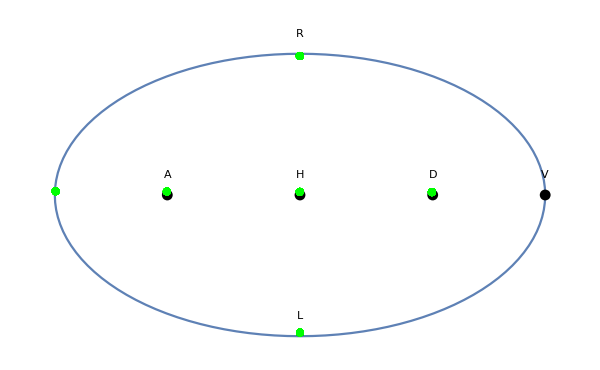

```mathematica
Show[ListPlot[Table[ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->Range[0.,2*Pi,2*Pi/120][[i]],az->Pi},{2}],{i,1,121}],Joined->{True,False}],ListPlot[Table[HammerCoordinates[blochlistStates[[i]]],{i,1,6}],PlotStyle->{PointSize[0.013],RGBColor[0,0,0]}],
ListPlot[Table[HammerCoordinates[BlochListH[[i]]],{i,1,Dimensions[BlochListH][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
ListPlot[Table[HammerCoordinates[BlochListV[[i]]],{i,1,Dimensions[BlochListV][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
ListPlot[Table[HammerCoordinates[BlochListD[[i]]],{i,1,Dimensions[BlochListD][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
ListPlot[Table[HammerCoordinates[BlochListA[[i]]],{i,1,Dimensions[BlochListA][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
ListPlot[Table[HammerCoordinates[BlochListR[[i]]],{i,1,Dimensions[BlochListR][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
ListPlot[Table[HammerCoordinates[BlochListL[[i]]],{i,1,Dimensions[BlochListL][[1]]}],PlotStyle->{PointSize[0.0095],RGBColor[0,1,0],Opacity[0.9]}],
Graphics[Style[Text["H",{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["V",{2 √2,0.2}],Black,Italic,30]],
Graphics[Style[Text["D",{2/(√(1+1/(√2))),0.2}],Black,Italic,30]],
Graphics[Style[Text["A",{-2/(√(1+1/(√2))),0.2}],Black,Italic,30]],
Graphics[Style[Text["R",{0,√2+0.2}],Black,Italic,30]],
Graphics[Style[Text["L",{0,-√2+0.2}],Black,Italic,30]],
PlotRange->All,Axes->False,ImageSize->600]
```

```mathematica
(* Average *)
```

```mathematica
(* Fidelity *)
Mean[Join[FidelityListH,FidelityListV,FidelityListD,FidelityListA,FidelityListR,FidelityListL]]
StandardDeviation[Join[FidelityListH,FidelityListV,FidelityListD,FidelityListA,FidelityListR,FidelityListL]]
```

{0.999596}

{0.000386041}

```mathematica
(* Purity *)
Mean[Join[PurityListH,PurityListV,PurityListD,PurityListA,PurityListR,PurityListL]]
StandardDeviation[Join[PurityListH,PurityListV,PurityListD,PurityListA,PurityListR,PurityListL]]
```

0.999786

0.000478223

```mathematica
(* Angle *)
Mean[Join[AnglesH,AnglesV,AnglesD,AnglesA,AnglesR,AnglesL]];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
StandardDeviation[Join[AnglesH,AnglesV,AnglesD,AnglesA,AnglesR,AnglesL]];
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]/2
```

0.965076 °

0.212406 °

```mathematica
(* States Bloch coordinates *)
(* H *)
```

```mathematica
Mean[Transpose[BlochListH][[1]]]
StandardDeviation[Transpose[BlochListH][[1]]]
Mean[Transpose[BlochListH][[2]]]
StandardDeviation[Transpose[BlochListH][[2]]]
Mean[Transpose[BlochListH][[3]]]
StandardDeviation[Transpose[BlochListH][[3]]]
```

0.99952

5.42335×10^-6

-0.00321469

0.00040235

0.0308086

0.000199288

```mathematica
(* V *)
```

```mathematica
Mean[Transpose[BlochListV][[1]]]
StandardDeviation[Transpose[BlochListV][[1]]]
Mean[Transpose[BlochListV][[2]]]
StandardDeviation[Transpose[BlochListV][[2]]]
Mean[Transpose[BlochListV][[3]]]
StandardDeviation[Transpose[BlochListV][[3]]]
```

-0.999566

4.0732×10^-6

-0.0119091

0.000780581

0.0269462

0.000339283

```mathematica
(* D *)
```

```mathematica
Mean[Transpose[BlochListD][[1]]]
StandardDeviation[Transpose[BlochListD][[1]]]
Mean[Transpose[BlochListD][[2]]]
StandardDeviation[Transpose[BlochListD][[2]]]
Mean[Transpose[BlochListD][[3]]]
StandardDeviation[Transpose[BlochListD][[3]]]
```

0.00993305

0.000922576

0.999599

6.62354×10^-6

0.0264946

0.000184617

```mathematica
(* A *)
```

```mathematica
Mean[Transpose[BlochListA][[1]]]
StandardDeviation[Transpose[BlochListA][[1]]]
Mean[Transpose[BlochListA][[2]]]
StandardDeviation[Transpose[BlochListA][[2]]]
Mean[Transpose[BlochListA][[3]]]
StandardDeviation[Transpose[BlochListA][[3]]]
```

-0.00555835

0.000860378

-0.999484

0.0000193461

0.0316211

0.000465012

```mathematica
(* R *)
```

```mathematica
Mean[Transpose[BlochListR][[1]]]
StandardDeviation[Transpose[BlochListR][[1]]]
Mean[Transpose[BlochListR][[2]]]
StandardDeviation[Transpose[BlochListR][[2]]]
Mean[Transpose[BlochListR][[3]]]
StandardDeviation[Transpose[BlochListR][[3]]]
```

0.031151

0.000447666

-0.00217176

0.00041028

0.999512

0.000013485

```mathematica
(* L *)
```

```mathematica
Mean[Transpose[BlochListL][[1]]]
StandardDeviation[Transpose[BlochListL][[1]]]
Mean[Transpose[BlochListL][[2]]]
StandardDeviation[Transpose[BlochListL][[2]]]
Mean[Transpose[BlochListL][[3]]]
StandardDeviation[Transpose[BlochListL][[3]]]
```

0.0499104

0.000525278

-0.000134867

0.0002042

-0.997469

0.0000240153